# Near-Axis Expansion for Isoprominence: Examples

This notebook is a companion to the paper CITE. The function names in this notebook are the same as in the paper.
It explores the two examples of near-axis, approximately isoprominent fields contained in the paper.

## Initialisation

Requirements: In order to run the examples the notebook IsoprominenceConditions.nb needs to first be run with order = 3 to generate hsols_3.wdx, Bdiv0_3.wdx.
These files must also be sitting in the same directory as this notebook.

### Mathematica Utility Functions

```mathematica
(* Package needed for Combinations[] function *)
Quiet[<<Combinatorica`]
```

```mathematica
(* function which takes output of Solve and turns functions into explicit Function commands *)
SolveToFunction[sols_]:=sols/.Rule[e_[s_],expr_]:>Rule[e,Function[S,expr/.s->S]]

(* Creates list of all monomials in X = {x,y,z,...} of order d *)
Monomials[X_,d_]:=Map[Times@@(X^#)&,Compositions[d,Length[X]]];

(* Generate an arbitrary homogeneous polynomial of degree d *)
HomPolynomial::usage = "HomPolynomial[{x,y,...},d,h] returns an arbitrary homogeneous polynomial of degree d in {x,y,...} with coefficient handle h. The option Coefficients->True will return the coefficients as a list in the form {poly,coeffs}";

Options[HomPolynomial] = {Coefficients->False};
HomPolynomial[X_,d_,h_,opts : OptionsPattern[]]:=Module[{terms,coeffs,polys,n},
n=Length[X];
terms = Monomials[X,d];
coeffs =(h@@#&/@Compositions[d,n]);
polys =coeffs.terms;

If[OptionValue[Coefficients],
Return[{polys,coeffs}],
Return[polys]
]
];

(* Generate an arbitrary polynomial of degree d *)
Polynomial::usage = "Polynomial[{x,y,...},d,h] returns an arbitrary polynomial of degree d in {x,y,...} with coefficient handle h. The option Coefficients->True will return the coefficients as a list in the form {poly,coeffs}";

Options[Polynomial] = {Coefficients->False};
Polynomial[X_,d_,h_,opts : OptionsPattern[]]:=Module[{polyinfo,poly,coeffs},
If[OptionValue[Coefficients],
polyinfo=Transpose[Function[i,HomPolynomial[X,i,h,Coefficients->True]]/@Range[0,d]];
poly=Plus@@polyinfo⟦1⟧;
coeffs=polyinfo⟦2⟧;
Return[{poly,coeffs}],

Plus@@Function[i,HomPolynomial[X,i,h]]/@Range[0,d]
]
];
```

```mathematica
(* For Taylor series expansions *)
Taylor::usage = "Taylor[vf, vars, k] produces the k-jet of the vector field vf in variables vars.";
Taylor[vf_,vars_,deg_]:=Module[{ctraf,vftemp,c},
	ctraf = Thread[vars->c vars];
	vftemp =Series[ vf/.ctraf,{c,0,deg}]//Normal;
	vftemp/.c->1
];

(* A common simplification that collects x,y terms and simplifies coefficients *)
Collectxy[expr_]:=Collect[expr/.Thread[{x,y}->ϵ{x,y}],ϵ,Collect[#,{x,y},Simplify]&]/.ϵ->1;
```

### Importing hsols

```mathematica
SetDirectory[NotebookDirectory[]];
hsols=Import["hsols_3.wdx"];
Bdiv0[]=Import["Bdiv0_3.wdx"];
```

## Examples

### Example 1

This is Example 1 of the paper. It is a degree 4 polynomial vector-field in x,y which satisfies isoprominence to order 3.

#### Equations defining the example

We choose B_0(s) = C_0 e^(2(F(s)-F(0))) such that 
F(s) = 1/10 cos(s), 	 F'(s) = -1/10sin(s).
This guarantees that Σ^- only intersects the magnetic axis at x=y=0 when s^*=0.

We choose the axis to be a simple circle so that κ(s) = κ_0 (const) and τ(s) = 0

The order = 3.

```mathematica
F[s_]:=1/10Cos[s];
Clear[F];
B0sub=B0->Function[s,Exp[ 2(F[s]-F[0])]];
Fsub=F->Function[s,1/10Cos[s]];
T=2π; (* The period of s-coordinate *)
order = 3;
```

```mathematica
(* Curve values *)
curveVals={κ->Function[s,κ0],τ->Function[s,0]};
```

```mathematica
(* Turning the isoprominent condition into a function substitution called hrules *)
hsolfun=SolveToFunction[hsols]//Flatten;
Thread[Rule[#⟦;;,1⟧,#⟦;;,2⟧//.hsolfun]]&/@hsols;
hrules=%/.B0'[st]->0//Flatten;
```

```mathematica
(* Substituing parameter values into hrules and taking s^*=0 *)
intconds=hrules/.B0sub/.curveVals/.Fsub/.st->0
```

{Bs[0,1][0]→0,Bs[1,0][0]→κ0,Bs[0,2][0]→1/8 (-(Δ[1][0])^2-(μ[1][0])^2),Bs[1,1][0]→1/4 Δ[1][0] (-μ[1][0]+ν[1][0]),Bs[2,0][0]→1/2 (2 κ0^2-1/4 (Δ[1][0])^2-1/4 (ν[1][0])^2),Bs[0,3][0]→1/12 (-3 Δ[1][0] Δ[2,1][0]-6 μ[1][0] μ[2][0]),Bs[1,2][0]→1/24 (-9 κ0 ((Δ[1][0])^2+(μ[1][0])^2)-2 (6 Δ[1][0] (Δ[2,0][0]+μ[2][0])+Δ[2,1][0] (6 μ[1][0]-3 ν[1][0]))),Bs[2,1][0]→1/12 (-3 Δ[2,0][0] (μ[1][0]-2 ν[1][0])-Δ[1][0] (6 Δ[2,1][0]+9 κ0 (μ[1][0]-ν[1][0])-6 ν[2][0])),Bs[3,0][0]→-125/6 (-(6 κ0^3)/125+1/500 (6 Δ[1][0] Δ[2,0][0]+9 κ0 ((Δ[1][0])^2+(ν[1][0])^2)+12 ν[1][0] ν[2][0]))}

The above is what needs to be true to satisfy isoprominence to order 3.
As per the paper, we choose the interpolations so that hrules is satisfied for all s, that is, the s-component of B is independent of s.
The result is BsRules which specifies the coefficients of x,y in B for isoprominence.

```mathematica
BsRules=intconds/.Bs[j_,k_][0]:>Bs[j,k][s];
BsRules=SolveToFunction[BsRules];
```

```mathematica
(* This checks that the isoprominent conditions have been met *)
(* It should evaluate to a vector of zeroes *)
intconds/.Rule->Subtract/.BsRules//Simplify
```

{0,0,0,0,0,0,0,0,0}

```mathematica
(* The B-field of example1 *)
Bexam=Collect[Bdiv0[]//.BsRules/.Thread[{x,y}->ϵ{x,y}],ϵ]/.ϵ->1;
```

```mathematica
(* Order 1 *)
(* Inputting the desired linear terms of B for example 1 in paper *)
funs1={μ[1]->Function[s,2B0[s](C[1] Exp[2F[s]])],ν[1]->Function[s,2 C[1]^-1 B0[s]Exp[-2F[s]](-((2π ι0)/T)^2+F''[s]-Δt[1]'[s]-(Δt[1][s]-F'[s])^2)],Δt[1]->Function[s,(2B0[s])^-1 Δ[1][s]]};
funs1=AppendTo[funs1,Δ[1]->Function[s,0]];
Bexam1=Collect[Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k>1:>0,ϵ]/.ϵ^k_/;k>1:>0//.funs1;
```

```mathematica
(* Double checking that the linear terms produce a harmonic oscillator in x with rotation ι0 *)
(* Out should be -ι0^2 x *)
tt=Taylor[Bexam1⟦2;;⟧/Bexam1⟦1⟧,{x,y},1]/.ϵ->1;
tt=Collect[tt,{x,y},FullSimplify];
ysol=Solve[x'[s]==tt⟦1⟧,y]⟦1⟧;
expr=D[tt⟦1⟧/.Thread[{x,y}->{x[s],y[s]}],s]/.y'[s]->tt⟦2⟧/.Thread[{x[s],y[s]}->{x,y}]/.ysol/.x'[s]->xp/.B0sub;
expr=Collect[expr,{x,xp},FullSimplify]
```

-x ι0^2

```mathematica
(* Order 2: set all free terms to 0 *)
Bexam2=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==2:>1/.ϵ->0//Simplify
funs2={Δ[2,__]:>Function[s,0],μ[2]->Function[s,0],ν[2]->Function[s,0]};
```

{1/8 (8 B0[s]-y^2 ((Δ[1][0])^2+(μ[1][0])^2)+2 x y Δ[1][0] (-μ[1][0]+ν[1][0])+x^2 (8 κ0^2-(Δ[1][0])^2-(ν[1][0])^2)),1/6 (3 x^2 Δ[2,0][s]+6 x y Δ[2,1][s]+6 y^2 μ[2][s]+x κ[s] (3 x Δ[1][s]+3 y μ[1][s]-x B0'[s])+2 x^2 B0[s] κ'[s]),1/6 (-6 x y Δ[2,0][s]-3 y^2 Δ[2,1][s]+6 x^2 ν[2][s]+x κ[s] (-3 y Δ[1][s]+3 x ν[1][s]-y B0'[s])+2 x y B0[s] κ'[s])}

```mathematica
(* order 3: set all free terms to 0 *)
Bexam3=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==3:>1/.ϵ->0;
funs3={Δ[3,__]:>Function[s,0],μ[3]->Function[s,0],ν[3]->Function[s,0]};
```

```mathematica
(* order 4: set all free terms to 0 *)
Bexam4=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==4:>1/.ϵ->0/.B0sub;
funs4={Δ[4,__]:>Function[s,0],μ[4]->Function[s,0],ν[4]->Function[s,0]};
```

```mathematica
(* Substituting all of the choices of free functions at each order to get the final example B-field, BexamFin *)BexamFin=Bexam//.funs1/.funs2/.funs3/.funs4/.B0sub/.Fsub/.curveVals;
BexamFin=Collect[BexamFin,ϵ,Collect[#,{x,y},Simplify]&]
```

{ⅇ^(1/5 (-1+Cos[s]))+1/2 x^2 (2 κ0^2-((1+10 ι0^2)^2)/(100 ⅇ^(2/5) C[1]^2))-1/2 x^3 κ0 (-2 κ0^2+(3 (1+10 ι0^2)^2)/(100 ⅇ^(2/5) C[1]^2))-1/2 ⅇ^(2/5) y^2 C[1]^2+x (κ0-3/2 ⅇ^(2/5) y^2 κ0 C[1]^2),ⅇ^(-1/5+(2 Cos[s])/5) y C[1]-1/6 ⅇ^(1/5 (-1+Cos[s])) x^4 κ0^3 Sin[s]+x (ⅇ^(-1/5+(2 Cos[s])/5) y κ0 C[1]+1/10 ⅇ^(1/5 (-1+Cos[s])) Sin[s])+x^2 (ⅇ^(-1/5+(2 Cos[s])/5) y κ0^2 C[1]+1/30 ⅇ^(1/5 (-1+Cos[s])) κ0 Sin[s])+x^3 (-3 ⅇ^(-1/5+(2 Cos[s])/5) y κ0^3 C[1]+1/30 ⅇ^(1/5 (-1+Cos[s])) κ0^2 Sin[s]),1/10 ⅇ^(1/5 (-1+Cos[s])) y Sin[s]+x ((-1-200 ι0^2-20 Cos[s]+Cos[2 s])/(200 ⅇ^(1/5) C[1])+1/30 ⅇ^(1/5 (-1+Cos[s])) y κ0 Sin[s])-(x^4 κ0^3 (100 ι0^2+10 Cos[s]+Sin[s]^2))/(100 ⅇ^(1/5) C[1])+x^2 (6 ⅇ^(-1/5+(2 Cos[s])/5) y^2 κ0^3 C[1]+1/30 ⅇ^(1/5 (-1+Cos[s])) y κ0^2 Sin[s]-(κ0 (100 ι0^2+10 Cos[s]+Sin[s]^2))/(100 ⅇ^(1/5) C[1]))+x^3 (5/6 ⅇ^(1/5 (-1+Cos[s])) y κ0^3 Sin[s]-(κ0^2 (100 ι0^2+10 Cos[s]+Sin[s]^2))/(100 ⅇ^(1/5) C[1]))}

#### Computing Poincare Section for choice of parameters

Currently C1, ι0 and κ0 are parameters for our first family of example fields.
We now make a particular choice of parameters and view the magnetic field.

```mathematica
(* The chosen parameter values *)
paramsub={C[1]->ι0,κ0->1,ι0->1/GoldenRatio};
```

```mathematica
(* The example vector field vf with params substituted *)
vf=BexamFin//.paramsub;
```

We will now compute the Poincare section at s=0

```mathematica
(* We will compute a Poincare section at s=0.
This is most easily done by taking time to be given by s, and considering B as a non-autonomous vector field with only x,y components.
This is vf2.
*)
vf2=vf⟦2;;⟧/vf⟦1⟧;
```

```mathematica
(* nsolve numerically solves the non-autonomous vector field vf2 with initial condition inits for s values between tmin and tmax *)nsolve[vf2_,inits_,{tmin_,tmax_}]:=NDSolve[Join[Thread[{x'[s],y'[s]}==(vf2/.Thread[{x,y}->{x[s],y[s]}])],Thread[{x[0],y[0]}==inits]],{x,y},{s,tmin,tmax}]⟦1⟧;
(* getpts[sol] will compute the points (x(s),y(s)) along sols for which s=0 mod 2π. That is, it will compute the orbit on the Poincare section of the numerical solution of vf2 sols *)
getpts[sol_]:=Transpose[{x[s],y[s]}/.sol/.s->(2π )Range[Ceiling[(x["Domain"]⟦1,1⟧)/(2π)]/.sol,Floor[(x["Domain"]⟦1,2⟧)/(2π)/.sol]]];
```

```mathematica
(* Running this cell will produce a plot of Poincare section.
Clicking in the plot will compute the orbit on the Poincare section of the initial condition from your mouse click *) Manipulate[z=getpts[Quiet[nsolve[vf2,#,{-300 2π,300 2π}]]]&/@u;
plt=ListPlot[z,PlotRange->{{-1,1},{-1,1}},ImageSize->1000,Background->White,PlotStyle->PointSize[0.003]],{{u,{}},Locator,Appearance->None,LocatorAutoCreate->All},{z,{},None}]
```

### Example 2

This is Example 2 of the paper. It is a degree 4 polynomial vector-field in x,y which satisfies isoprominence to order 3.

#### Equations defining the example

We choose B_0(s) = C_0 e^(2(F(s)-F(0))) such that 
F(s) = a cos(s)+b cos(2s), 	 F'(s) = -a sin(s) -2b sin(2s),
where 0 < a < 4b. This guarantees that Σ^- intersects the magnetic axis at x=y=0 when s^*=0 and π.

We choose the axis to be a simple circle so that κ(s) = κ_0 (const) and τ(s) = 0

```mathematica
F[s_]:=a Cos[s]+b Cos[2s];
Clear[F];
B0sub=B0->Function[s,Exp[ 2(F[s]-F[0])]];
Fsub=F->Function[s,a Cos[s]+b Cos[2s]];
T=2π; (* The period of s-coordinate *)
order=3;
```

```mathematica
(* Curve values *)
curveVals={κ->Function[s,κ0],τ->Function[s,0]};
```

```mathematica
hsolfun=SolveToFunction[hsols]//Flatten;
Thread[Rule[#⟦;;,1⟧,#⟦;;,2⟧//.hsolfun]]&/@hsols;
hrules=%/.B0'[st]->0//Flatten;
```

```mathematica
(* The two conditions for isoprominence. Each stem from the stratum at st=0 or π *)
intconds1=hrules/.B0sub/.curveVals/.Fsub/.st->0
intconds2=hrules/.B0sub/.curveVals/.Fsub/.st->π
```

{Bs[0,1][0]→0,Bs[1,0][0]→κ0,Bs[0,2][0]→1/8 (-(Δ[1][0])^2-(μ[1][0])^2),Bs[1,1][0]→1/4 Δ[1][0] (-μ[1][0]+ν[1][0]),Bs[2,0][0]→1/2 (2 κ0^2-1/4 (Δ[1][0])^2-1/4 (ν[1][0])^2),Bs[0,3][0]→1/12 (-3 Δ[1][0] Δ[2,1][0]-6 μ[1][0] μ[2][0]),Bs[1,2][0]→1/24 (-9 κ0 ((Δ[1][0])^2+(μ[1][0])^2)-2 (6 Δ[1][0] (Δ[2,0][0]+μ[2][0])+Δ[2,1][0] (6 μ[1][0]-3 ν[1][0]))),Bs[2,1][0]→1/12 (-3 Δ[2,0][0] (μ[1][0]-2 ν[1][0])-Δ[1][0] (6 Δ[2,1][0]+9 κ0 (μ[1][0]-ν[1][0])-6 ν[2][0])),Bs[3,0][0]→(48 (-a-4 b)^3 κ0^3-2 (-a-4 b)^3 (6 Δ[1][0] Δ[2,0][0]+9 κ0 ((Δ[1][0])^2+(ν[1][0])^2)+12 ν[1][0] ν[2][0]))/(48 (-a-4 b)^3)}

{Bs[0,1][π]→0,Bs[1,0][π]→ⅇ^(-4 a) κ0,Bs[0,2][π]→-1/8 ⅇ^(4 a) ((Δ[1][π])^2+(μ[1][π])^2),Bs[1,1][π]→1/4 ⅇ^(4 a) Δ[1][π] (-μ[1][π]+ν[1][π]),Bs[2,0][π]→1/2 (2 ⅇ^(-4 a) κ0^2-1/4 ⅇ^(4 a) (Δ[1][π])^2-1/4 ⅇ^(4 a) (ν[1][π])^2),Bs[0,3][π]→1/12 ⅇ^(4 a) (-3 Δ[1][π] Δ[2,1][π]-6 μ[1][π] μ[2][π]),Bs[1,2][π]→-1/24 ⅇ^(4 a) (9 κ0 ((Δ[1][π])^2+(μ[1][π])^2)+2 (6 Δ[1][π] (Δ[2,0][π]+μ[2][π])+Δ[2,1][π] (6 μ[1][π]-3 ν[1][π]))),Bs[2,1][π]→-1/12 ⅇ^(4 a) (3 Δ[2,0][π] (μ[1][π]-2 ν[1][π])+Δ[1][π] (6 Δ[2,1][π]+9 κ0 (μ[1][π]-ν[1][π])-6 ν[2][π])),Bs[3,0][π]→(ⅇ^(16 a) (48 (a-4 b)^3 ⅇ^(-20 a) κ0^3-2 (a-4 b)^3 ⅇ^(-12 a) (6 Δ[1][π] Δ[2,0][π]+9 κ0 ((Δ[1][π])^2+(ν[1][π])^2)+12 ν[1][π] ν[2][π])))/(48 (a-4 b)^3)}

The above is what needs to be true for isoprominence of order 3. 
This will define the coefficient values for the s-component of Bs at st1 = 0 and st2 = π.
We will choose an interpolation so that Bs =  1/2 Bs[0](1+Cos[s])+1/2Bs[π](1-Cos[s])

```mathematica
(* generate all the coefficients in Bs *)
BsCoeffs=Table[(Bs@@#)[s]&/@Compositions[i,2],{i,1,order}]//Flatten;
```

```mathematica
Bs0=BsCoeffs/.s->0/.intconds1;
Bs1=BsCoeffs/.s->π/.intconds2;
Bsinterp=1/2(1+Cos[s])Bs0+1/2(1-Cos[s])Bs1//FullSimplify (* takes a while to simplify... *)
```

{0,1/2 κ0 (1-ⅇ^(-4 a) (-1+Cos[s])+Cos[s]),1/16 (-(1+Cos[s]) ((Δ[1][0])^2+(μ[1][0])^2)+ⅇ^(4 a) (-1+Cos[s]) ((Δ[1][π])^2+(μ[1][π])^2)),1/8 ((1+Cos[s]) Δ[1][0] (-μ[1][0]+ν[1][0])+ⅇ^(4 a) (-1+Cos[s]) Δ[1][π] (μ[1][π]-ν[1][π])),1/16 ((1+Cos[s]) (8 κ0^2-(Δ[1][0])^2-(ν[1][0])^2)+ⅇ^(-4 a) (-1+Cos[s]) (-8 κ0^2+ⅇ^(8 a) ((Δ[1][π])^2+(ν[1][π])^2))),1/8 (-(1+Cos[s]) (Δ[1][0] Δ[2,1][0]+2 μ[1][0] μ[2][0])+ⅇ^(4 a) (-1+Cos[s]) (Δ[1][π] Δ[2,1][π]+2 μ[1][π] μ[2][π])),1/48 ((1+Cos[s]) (-9 κ0 ((Δ[1][0])^2+(μ[1][0])^2)-12 Δ[1][0] (Δ[2,0][0]+μ[2][0])+6 Δ[2,1][0] (-2 μ[1][0]+ν[1][0]))-ⅇ^(4 a) (1-Cos[s]) (9 κ0 ((Δ[1][π])^2+(μ[1][π])^2)+12 Δ[1][π] (Δ[2,0][π]+μ[2][π])+6 Δ[2,1][π] (2 μ[1][π]-ν[1][π]))),1/24 ((1+Cos[s]) (-3 Δ[2,0][0] (μ[1][0]-2 ν[1][0])+Δ[1][0] (-6 Δ[2,1][0]-9 κ0 μ[1][0]+9 κ0 ν[1][0]+6 ν[2][0]))-ⅇ^(4 a) (1-Cos[s]) (3 Δ[2,0][π] (μ[1][π]-2 ν[1][π])+Δ[1][π] (6 Δ[2,1][π]+9 κ0 μ[1][π]-9 κ0 ν[1][π]-6 ν[2][π]))),1/96 (6 (1+Cos[s]) (8 κ0^3-3 κ0 ((Δ[1][0])^2+(ν[1][0])^2)-2 (Δ[1][0] Δ[2,0][0]+2 ν[1][0] ν[2][0]))+6 ⅇ^(-4 a) (-1+Cos[s]) (-8 κ0^3+ⅇ^(8 a) (2 Δ[1][π] Δ[2,0][π]+3 κ0 ((Δ[1][π])^2+(ν[1][π])^2)+4 ν[1][π] ν[2][π])))}

```mathematica
(* Rules for Bs so that interpolation holds and consequently isoprominence *)
BsRules=Thread[BsCoeffs->Bsinterp]//SolveToFunction;
```

```mathematica
(* Checking that both the isoprominence conditions have been satisfied*)
(* Output should be two vectors of zeroes *)
intconds1/.Rule->Subtract/.BsRules//Simplify
intconds2/.Rule->Subtract/.BsRules//Simplify
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

```mathematica
(* The B-field for example 2*)
Bexam=Collect[Bdiv0[]//.BsRules/.Thread[{x,y}->ϵ{x,y}],ϵ]/.ϵ->1;
```

```mathematica
(* Getting linearisation as desired *)
funs1={μ[1]->Function[s,2B0[s](C[1] Exp[2F[s]])],ν[1]->Function[s,2 C[1]^-1 B0[s]Exp[-2F[s]](-((2π ι0)/T)^2+F''[s]-Δt[1]'[s]-(Δt[1][s]-F'[s])^2)],Δt[1]->Function[s,(2B0[s])^-1 Δ[1][s]]};
funs1=AppendTo[funs1,Δ[1]->Function[s,0]];
Bexam1=Collect[Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k>1:>0,ϵ]/.ϵ^k_/;k>1:>0//.funs1;
```

```mathematica
(* Checking we will get the harmonic oscillator for x *)
tt=Taylor[Bexam1⟦2;;⟧/Bexam1⟦1⟧,{x,y},1]/.ϵ->1;
tt=Collect[%,{x,y},FullSimplify];
ysol=Solve[x'[s]==tt⟦1⟧,y]⟦1⟧;
expr=D[tt⟦1⟧/.Thread[{x,y}->{x[s],y[s]}],s]/.y'[s]->tt⟦2⟧/.Thread[{x[s],y[s]}->{x,y}]/.ysol/.x'[s]->xp/.B0sub;
expr=Collect[expr,{x,xp},FullSimplify]
```

-x ι0^2

```mathematica
(* order 2: set all free terms to 0 *)
Bexam2=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==2:>1/.ϵ->0//Simplify;
funs2={Δ[2,__]:>Function[s,0],μ[2]->Function[s,0],ν[2]->Function[s,0]};
```

```mathematica
(* order 3: set all free terms to 0 *)
Bexam3=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==3:>1/.ϵ->0;
funs3={Δ[3,__]:>Function[s,0],μ[3]->Function[s,0],ν[3]->Function[s,0]};
```

```mathematica
(* order 4: set all free terms to 0 *)
Bexam4=Bexam/.Thread[{x,y}->ϵ{x,y}]/.ϵ^k_/;k==4:>1/.ϵ->0/.B0sub;
funs4={Δ[4,__]:>Function[s,0],μ[4]->Function[s,0],ν[4]->Function[s,0]};
```

```mathematica
(* Substituting all of the choices of free functions at each order to get the final example B-field, BexamFin *)BexamFin=Bexam//.funs1/.funs2/.funs3/.funs4/.B0sub/.Fsub/.curveVals;
BexamFin=Collect[BexamFin,ϵ,Collect[#,{x,y},Simplify]&]
```

{ⅇ^(-4 (a+2 b+2 b Cos[s]) Sin[s/2]^2)-1/4 ⅇ^(-8 a+4 b) y^2 C[1]^2 (1+ⅇ^(12 a)+(-1+ⅇ^(12 a)) Cos[s])-(x^2 (ⅇ^(-4 a) (ⅇ^(4 a-4 b) (-a+4 b+ι0^2)^2-2 κ0^2 C[1]^2) (1-Cos[s])+(ⅇ^(-4 (a+b)) (a+4 b+ι0^2)^2-2 κ0^2 C[1]^2) (1+Cos[s])))/(4 C[1]^2)-(x^3 (ⅇ^(-4 a) (3 ⅇ^(4 a-4 b) (-a+4 b+ι0^2)^2 κ0-2 κ0^3 C[1]^2) (1-Cos[s])+(3 ⅇ^(-4 (a+b)) (a+4 b+ι0^2)^2 κ0-2 κ0^3 C[1]^2) (1+Cos[s])))/(4 C[1]^2)+x (1/2 κ0 (1-ⅇ^(-4 a) (-1+Cos[s])+Cos[s])-3/4 ⅇ^(-8 a+4 b) y^2 κ0 C[1]^2 (1+ⅇ^(12 a)+(-1+ⅇ^(12 a)) Cos[s])),ⅇ^(4 a Cos[s]-2 (a+b-2 b Cos[2 s])) y C[1]-1/(48 C[1]^2)ⅇ^(-4 (a+b)) x^4 κ0 (3 a^2 (-1+ⅇ^(4 a))-24 a b (1+ⅇ^(4 a))-6 a (1+ⅇ^(4 a)) ι0^2+80 a ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2+(-1+ⅇ^(4 a)) (48 b^2+24 b ι0^2+3 ι0^4+16 ⅇ^(4 b) κ0^2 C[1]^2)+320 b ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2 Cos[s]) Sin[s]+x (ⅇ^(-2 (a+b-2 a Cos[s]-2 b Cos[2 s])) y κ0 C[1]-1/16 ⅇ^(-8 a+4 b) (-1+ⅇ^(12 a)) y^2 C[1]^2 Sin[s]+ⅇ^(-2 (a+b-a Cos[s]-b Cos[2 s])) (a+4 b Cos[s]) Sin[s])+x^3 (-3 ⅇ^(-2 (a+b-2 a Cos[s]-2 b Cos[2 s])) y κ0^3 C[1]+1/(48 C[1]^2)ⅇ^(-4 (a+b)) (3 a^2 (-1+ⅇ^(4 a))+(-1+ⅇ^(4 a)) (48 b^2+24 b ι0^2+3 ι0^4+8 ⅇ^(4 b) κ0^2 C[1]^2)-2 a (12 b (1+ⅇ^(4 a))+3 (1+ⅇ^(4 a)) ι0^2-8 ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2)+64 b ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2 Cos[s]) Sin[s])+x^2 (ⅇ^(-2 (a+b-2 a Cos[s]-2 b Cos[2 s])) y κ0^2 C[1]+1/16 ⅇ^(-8 a+4 b) (-1+ⅇ^(12 a)) y^2 κ0 C[1]^2 Sin[s]+1/6 κ0 (1-ⅇ^(-4 a)+2 ⅇ^(-2 (a+b-a Cos[s]-b Cos[2 s])) (a+4 b Cos[s])) Sin[s]),-1/16 ⅇ^(-8 a+4 b) (-1+ⅇ^(12 a)) y^3 C[1]^2 Sin[s]+ⅇ^(-2 (a+b-a Cos[s]-b Cos[2 s])) y (a+4 b Cos[s]) Sin[s]-(ⅇ^(-2 (a+b)) x^4 κ0^3 (ι0^2+4 b Cos[2 s]+a^2 Sin[s]^2+Cos[s] (a+8 a b Sin[s]^2)+4 b^2 Sin[2 s]^2))/C[1]+x (-5/16 ⅇ^(-8 a+4 b) (-1+ⅇ^(12 a)) y^3 κ0 C[1]^2 Sin[s]+1/6 y κ0 (1-ⅇ^(-4 a)+2 ⅇ^(-2 (a+b-a Cos[s]-b Cos[2 s])) (a+4 b Cos[s])) Sin[s]-(ⅇ^(-2 (a+b)) (ι0^2+4 b Cos[2 s]+a^2 Sin[s]^2+Cos[s] (a+8 a b Sin[s]^2)+4 b^2 Sin[2 s]^2))/C[1])+x^2 (6 ⅇ^(-2 (a+b-2 a Cos[s]-2 b Cos[2 s])) y^2 κ0^3 C[1]+1/(48 C[1]^2)ⅇ^(-4 (a+b)) y (3 a^2 (-1+ⅇ^(4 a))+(-1+ⅇ^(4 a)) (48 b^2+24 b ι0^2+3 ι0^4+8 ⅇ^(4 b) κ0^2 C[1]^2)-2 a (12 b (1+ⅇ^(4 a))+3 (1+ⅇ^(4 a)) ι0^2-8 ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2)+64 b ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2 Cos[s]) Sin[s]-(ⅇ^(-2 (a+b)) κ0 (ι0^2+4 b Cos[2 s]+a^2 Sin[s]^2+Cos[s] (a+8 a b Sin[s]^2)+4 b^2 Sin[2 s]^2))/C[1])+x^3 (1/(48 C[1]^2)ⅇ^(-4 (a+b)) y κ0 (51 a^2 (-1+ⅇ^(4 a))+(-1+ⅇ^(4 a)) (816 b^2+408 b ι0^2+51 ι0^4+104 ⅇ^(4 b) κ0^2 C[1]^2)-2 a (204 b (1+ⅇ^(4 a))+51 (1+ⅇ^(4 a)) ι0^2-200 ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2)+1600 b ⅇ^(2 (a+b+a Cos[s]+b Cos[2 s])) κ0^2 C[1]^2 Cos[s]) Sin[s]-(ⅇ^(-2 (a+b)) κ0^2 (ι0^2+4 b Cos[2 s]+a^2 Sin[s]^2+Cos[s] (a+8 a b Sin[s]^2)+4 b^2 Sin[2 s]^2))/C[1])}

#### Computing Poincare Section for choice of parameters

Currently C1, ι0, κ0, a and b are parameters for our second family of example fields.
  We now make a particular choice of parameters and view the magnetic field.

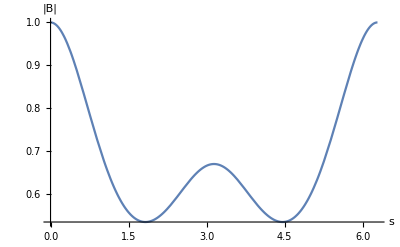

```mathematica
(* Note that 0 < a < 4b for two maxima *)
paramsub={C[1]->ι0,κ0->1,ι0->1/GoldenRatio,a->1/10,b->1/10};
(* A plot of the on-axis magnetic field strength *)
Plot[B0[s]/.B0sub/.Fsub//.paramsub,{s,0,2π},AxesLabel->{"s","|B|"}]
```

We will now compute the Poincare section at s=0

```mathematica
vf=BexamFin//.paramsub;
(* We will compute a Poincare section at s=0.
This is most easily done by taking time to be given by s, and considering B as a non-autonomous vector field with only x,y components.
This is vf2.
*)
vf2exam2=vf⟦2;;⟧/vf⟦1⟧;
```

```mathematica
(* nsolve numerically solves the non-autonomous vector field vf2 with initial condition inits for s values between tmin and tmax *)
nsolve[vf2_,inits_,{tmin_,tmax_}]:=NDSolve[Join[Thread[{x'[s],y'[s]}==(vf2/.Thread[{x,y}->{x[s],y[s]}])],Thread[{x[0],y[0]}==inits]],{x,y},{s,tmin,tmax}]⟦1⟧;
```

```mathematica
(* getpts[sol] will compute the points (x(s),y(s)) along sols for which s=0 mod 2π. That is, it will compute the orbit on the Poincare section of the numerical solution of vf2 sols *)
getpts[sol_]:=Transpose[{x[s],y[s]}/.sol/.s->(2π )Range[Ceiling[(x["Domain"]⟦1,1⟧)/(2π)]/.sol,Floor[(x["Domain"]⟦1,2⟧)/(2π)/.sol]]];
```

```mathematica
(* Running this cell will produce a plot of Poincare section.
Clicking in the plot will compute the orbit on the Poincare section of the initial condition from your mouse click *) 
Manipulate[z=getpts[Quiet[nsolve[vf2exam2,#,{-300 2π,300 2π}]]]&/@u;
plt=ListPlot[z,PlotRange->{{-1,1},{-1,1}},ImageSize->1000,Background->White,PlotStyle->PointSize[0.003]],{{u,{}},Locator,Appearance->None,LocatorAutoCreate->All},{z,{},None}]
```